```mathematica
Needs["OpenCLLink`"]

FetchData[filename_]:=  Import[NotebookDirectory[]<>"../data/simulation/"<>filename];
ExportData[filename_, data_]:= Export[NotebookDirectory[]<>"../data/simulation/"<>filename, data];
```

## TEST

```mathematica
{width,height}={256,256};
jset=OpenCLMemoryAllocate[_Integer,{height,width}];
MCalc=OpenCLFunctionLoad[
File[NotebookDirectory[]<>"sim.cl"],
"mandelbrot",
{
{_Integer,_,"Output"},
_Integer,
_Integer,
_Integer
},{16,16},"Defines"->{"MAX_ITERATIONS"->8},
"ShellOutputFunction"->Print
];
```

(): Warning: Function mandelbrot is a kernel, so overriding noinline attribute. The function may be inlined when called.

```mathematica
Manipulate[
MCalc[jset,width,height, depth];
ReliefPlot[
OpenCLMemoryGet[jset],
ImageSize->256,
ColorFunction->"SunsetColors",
PerformanceGoal->"Quality"
],
{depth,10,256, 1}
]
```

OpenCLMemoryGet::gethdfld: OpenCLLink was not able to get memory handle with head Symbol, required head is OpenCLMemory.

ReliefPlot::input: Argument OpenCLMemoryGet[jset] at position 1 is not a 2 x 2 or larger numerical matrix of real values.

## Single update simulation

```mathematica
(*On[Assert]*)

ClearAll["Pop"];
SetAttributes[Pop,HoldFirst];
Pop[list_]:=With[{item=list[[1]]},list=Delete[list,1];item];

ClearAll["SimulateSingle"];
SimulateSingle[rateMatrix_, nodeThresholds_, startingAgentPositions_, maxSteps_] := Module[{MoveAgents, AreThereFailures , ComputeAvalancheSize, i, nNodes, nAgents, carCountsByNode, agentPositions, possibleAgentPositions, failedNodes},
nNodes = Length[rateMatrix];
If[nNodes != Length[nodeThresholds], Return[$Failed]];

possibleAgentPositions = Table[i, {i, 1, nNodes}];
nAgents = Length[agentPositions];
agentPositions = startingAgentPositions;	

MoveAgents[] := Module[{},
agentPositions = (
Assert[Total[rateMatrix[[;;, #]]] == 1];
RandomChoice[rateMatrix[[;;, #]]->possibleAgentPositions ]
) &/@ agentPositions;
];

AreThereFailures[] := Module[{},
carCountsByNode = Count[agentPositions, #] &/@ Table[i, {i, 1, nNodes}];
failedNodes = Append[(Transpose@Position[# < 0 &/@ (nodeThresholds -carCountsByNode ), True]), {}][[1]];

If[Length[failedNodes]>0, Return[True]];
False
];

ComputeAvalancheSize[node_] := Module[{avalancheSize, carCount, avalancheCarCounts, adjacentNodes, nodesToCheck, lockedNodes, currentNode, newNode, transitionProbabilities},
nodesToCheck = {node};
lockedNodes = {};
avalancheCarCounts = carCountsByNode;


While[Length@nodesToCheck >0,
currentNode = Pop[nodesToCheck];
Assert[avalancheCarCounts[[currentNode]] >0, "carCount"];

If[nodeThresholds[[currentNode]] -avalancheCarCounts[[currentNode]] >=0, Continue[]];

AppendTo[lockedNodes, currentNode];

If[Length@lockedNodes == nNodes, Break[]];

transitionProbabilities = Normal@rateMatrix[[currentNode]];
(transitionProbabilities[[#]] = 0 )&/@ lockedNodes;

(* If there is nowhere to go, we just lock this node and no transfer*)
If[Total@transitionProbabilities == 0,
Continue[];
];

transitionProbabilities /= Total[transitionProbabilities];

For[carCount = avalancheCarCounts[[currentNode]], carCount >0, carCount--,
Assert[nNodes == Length@transitionProbabilities, "nNodes"];

newNode = RandomChoice[transitionProbabilities->Table[x, {x, 1, nNodes}]];

Assert[newNode != currentNode, "currentNode"];
Assert[!MemberQ[lockedNodes, newNode], "lockedNodes"];
If[!MemberQ[nodesToCheck, newNode], AppendTo[nodesToCheck, newNode]];

avalancheCarCounts[[newNode]]++;
avalancheCarCounts[[currentNode]]--;
];
];

Assert[Total[avalancheCarCounts] == Total[carCountsByNode]];

Return[{node,Length@lockedNodes}];
];

For[i=1, i<=maxSteps,  i++, 
MoveAgents[];

If[!AreThereFailures[], Continue[]];
Break[];
];

If[Length@failedNodes == 0, Return[{}]];

Map[ComputeAvalancheSize, failedNodes]
];
```

## Generate agents

```mathematica
ClearAll["GenerateAgentsUniform"];
GenerateAgentsUniform[nAgents_,nNodes_]:=Table[RandomInteger[{1,nNodes}],nAgents];
```

## Simulation Code

```mathematica
g = FetchData["g.mx"];
w = FetchData["w-naive.mx"];
s = GenerateAgentsUniform[1000, VertexCount@g];
c = FetchData["thresholds.mx"];
f = FetchData["flows.mx"];

t = 20;
sampleCount = 30;
```

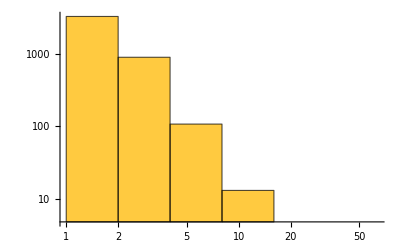

```mathematica
(*;;,;;,2 Selects avalanche size,;;,;;,1 selects start node*)
avalancheSizes=Flatten[ParallelTable[SimulateSingle[w,c,s,t][[;;, 2]],sampleCount]];
Histogram[avalancheSizes,{PowerRange[1, 100, 2]},  ScalingFunctions->{"Log", "Log"}, PlotRange->Full ]
```